# VREDNOST AMERIŠKEGA DOLARJA SKOZI ČAS

## Pripravil: Tin Šebenik, ROM, 2021/22

## PRIDOBIVANJE PODATKOV

Za naslov moje naloge sem si izbral vrednost ameriškega dolarja skozi čas. Ta naslov sem si izbral, ker se mi zdi dokaj aktualen, še posebaj trenutno, ko sta si z našo valuto evrom več ali manj enakovredna. Vse prikazane podatke sem dobil iz raznih spletnih strani. Vse povezave do teh spletnih strani bodo napisane spodaj.

```mathematica
Hyperlink["https://www.officialdata.org/us/inflation/1800?amount=1"]
```

https://www.officialdata.org/us/inflation/1800?amount=1

```mathematica
Hyperlink["https://www.officialdata.org/europe/inflation/1996?amount=1"]
```

https://www.officialdata.org/europe/inflation/1996?amount=1

```mathematica
Hyperlink["https://www.visualcapitalist.com/purchasing-power-of-the-u-s-dollar-over-time/"]
```

https://www.visualcapitalist.com/purchasing-power-of-the-u-s-dollar-over-time/

```mathematica
Hyperlink["https://fred.stlouisfed.org/series/M2SL"]
```

https://fred.stlouisfed.org/series/M2SL

```mathematica
vrednostUSD = Import["C:\\Users\\tin20\\Desktop\\ROM\\vrednostUSD.xlsx", "Dataset"];
```

```mathematica
vrednostEUR = Import["C:\\Users\\tin20\\Desktop\\ROM\\vrednostEUR.xlsx", "Dataset"];
```

```mathematica
kupnavrednostUSD = Import["C:\\Users\\tin20\\Desktop\\ROM\\kupnavrUSD.xlsx", "Dataset"];
```

## UVOD

Prvo malo na hitro o ameriškem dolarju . Pomembno je, da se reče ameriški dolar, saj obstaja več različnih, kot so na primer avstralski dolar, novozelandski dolar, itd . Kot pove ime, je uradna valuta Združenih držav Amerike . V drugih državah pa pogosto služi kot valuta državnih rezerv.

```mathematica
wiki = TextSentences[WikipediaData["United States dollar"]][[;;3]];
```

```mathematica
TextTranslation[wiki, #]&/@{"Slovenian"}
```

{{Ameriški dolar (simbol: $; oznaka: USD; prav tako okrajšava US$ ali ameriški dolar, da ga razloči od drugih valut, denominiranih z dolarjem; imenuje se dolar, ameriški dolar, ameriški dolar ali kolokvialno buck) je uradna valuta ZDA in več drugih držav.,Zakon o kovancih iz leta 1792 je uvedel ameriški dolar v skladu s španskim srebrnim dolarjem, ga razdelil na 100 centov in odobril kovanje kovancev, denominiranih v dolarjih in centih.,Bankovci v ZDA so izdani v obliki bankovcev zveznih rezerv, popularno imenovanih greenbacks zaradi svoje pretežno zelene barve.}}

## VREDNOST USD IN EUR SKOZI ČAS

### USD

```mathematica
SeznamVrednostiUSD = Table[vrednostUSD[[1]][[i]][[2]], {i, 2, Length[vrednostUSD[[1]]]}];
```

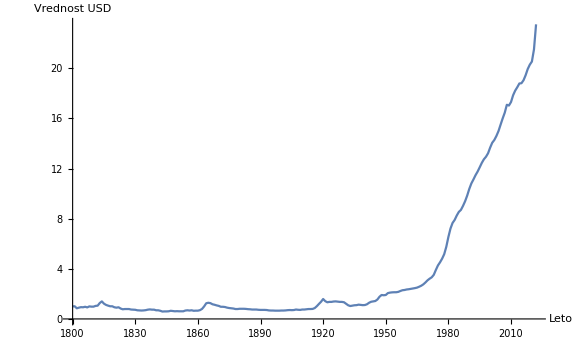

```mathematica
vrUSD = ListPlot[{SeznamVrednostiUSD}, DataRange->{1800,2022}, ImageSize->Large, AxesLabel->{"Leto","Vrednost USD"},Joined->True, AxesOrigin->{1800, 0}]
```

### EUR

Za evro sem našel podatke za leta 1996 in naprej.

```mathematica
vrUSD2 = ListPlot[{SeznamVrednostiUSD}, DataRange->{1996,2022}, ImageSize->Large, AxesLabel->{"Leto","Vrednost USD"}, Joined->True, AxesOrigin->{1996,0}];
```

```mathematica
SeznamVrednostiEUR = Table[vrednostEUR[[1]][[i]][[2]], {i, 2, Length[vrednostEUR[[1]]]}];
```

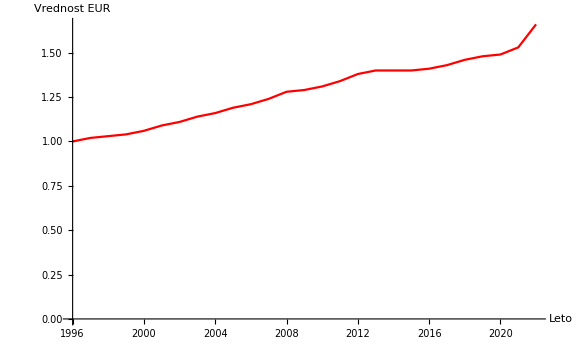

```mathematica
vrEUR = ListPlot[{SeznamVrednostiEUR}, DataRange->{1996,2022}, ImageSize->Large, AxesLabel->{"Leto","Vrednost EUR"}, PlotStyle->Red , Joined->True,AxesOrigin->{1996,0}]
```

### PRIMERJAVA VREDNOSTI USD IN EUR OD LETA 1996 DO 2022

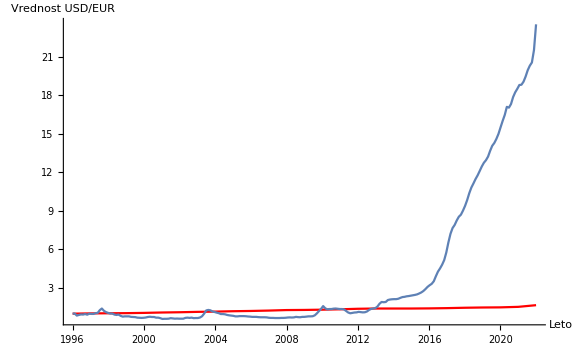

```mathematica
Show[vrEUR, vrUSD2, PlotRange->Automatic, AxesLabel->{"Leto", "Vrednost USD/EUR"}, AxesOrigin->{1996,0}]
```

### KUPNA VREDNOST AMERIŠKEGA DOLARJA SKOZI LETA

```mathematica
xkup = Table[kupnavrednostUSD[[1]][[i]][[1]], {i, 2, Length[kupnavrednostUSD[[1]]]}]
```

{,,,,,,,,,,}

```mathematica
ykup = Table[kupnavrednostUSD[[1]][[i]][[2]], {i, 2, Length[kupnavrednostUSD[[1]]]}]
```

{,,,,,,,,,,}

```mathematica
kupnavr = Transpose[{xkup,ykup}]
```

{{,},{,},{,},{,},{,},{,},{,},{,},{,},{,},{,}}

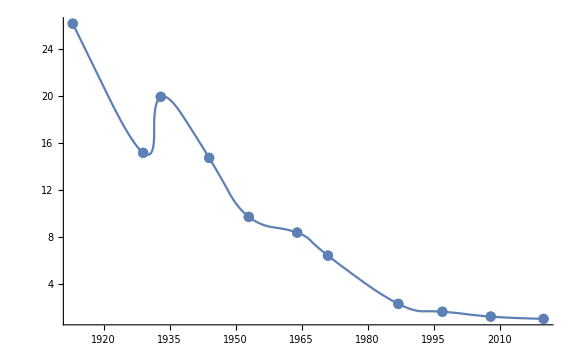

```mathematica
ListPlot[kupnavr, Mesh->Full, Joined->True,PlotRange->All,InterpolationOrder->2, ImageSize->Large, AxesOrigin->{1913,0}]
```

#### DEJAVNIKI, KI SO IMELI VEČJI VPLIV NA VREDNOST AMERIŠKEGA DOLARJA

```mathematica
dejavniki = Import["C:\\Users\\tin20\\Desktop\\ROM\\dejavniki.xlsx", "Dataset"]
```

{,}

1913

```mathematica
fedressys = TextSentences[WikipediaData["Federal Reserve"]][[;;2]];
```

```mathematica
TextTranslation[fedressys, #]&/@{"Slovenian"}
```

{{Sistem zveznih rezerv (znan tudi kot Zvezne rezerve ali preprosto Fed) je centralni bančni sistem Združenih držav Amerike.,Ustanovljena je bila 23. decembra 1913 z sprejetjem Zakona o zveznih rezervah, potem ko je vrsta finančnih panike (zlasti panika iz leta 1907) pripeljala do želje po centralnem nadzoru monetarnega sistema, da bi se ublažile finančne krize.}}

1929

```mathematica
stockcrash = TextSentences[WikipediaData["Wall Street Crash of 1929"]][[;;4]];
```

```mathematica
TextTranslation[stockcrash, #]&/@{"Slovenian"}
```

{{Wall Street Crash leta 1929, znan tudi kot Velika nesreča, je bila velika ameriška borzni nesreča, ki se je zgodila jeseni 1929.,Začelo se je septembra, končalo pa se je konec oktobra, ko so se zrušile cene delnic na newyorški borzi.,To je bil najbolj uničujoč borzni trk v zgodovini ZDA, ko se je upošteval celoten obseg in trajanje njenih posljedkov.,Velika nesreča je večinoma povezana z 24. oktobrom 1929, imenovanim Črni četrtek, dan največje prodaje delnic v zgodovini ZDA, in 29. oktober 1929, imenovan Črni torek, ko so vlagatelji v enem dnevu trgovali z nekaj 16 milijoni delnic na newyorški borzi.}}

1933

```mathematica
goldreserve = TextSentences[WikipediaData["Gold Reserve Act"]][[;;2]];
```

```mathematica
TextTranslation[goldreserve, #]&/@{"Slovenian"}
```

{{Zakon Združenih držav Amerike o zlatih rezervah z dne 30.,Ministrstvo za finance in finančne institucije je tudi prepovedalo odkup dolarskih bankovcev za zlato, ustanovilo sklad za stabilizacijo borze pod nadzorom finančnega zaklada za nadzor nad vrednostjo dolarjev brez pomoči (ali odobritve) zveznih rezerv in pooblastilo predsednika, da z razglasitvijo določi zlato vrednost dolarja.}}

1971

```mathematica
goldstandard = TextSentences[WikipediaData["Nixon shock"]][[;;1]];
```

```mathematica
TextTranslation[goldstandard, #]&/@{"Slovenian"}
```

{{Nixonov šok je bil niz gospodarskih ukrepov, ki jih je leta 1971 sprejel predsednik Združenih držav Amerike Richard Nixon, kot odziv na naraščajočo inflacijo, med katerimi so bili najpomembnejši zamrznitev plač in cen, nadomestki pri uvozu ter enostranska odpoved neposredne mednarodne konvertibilnosti ameriških dolarjev v zlato.}}

2008

```mathematica
fincrisis = TextSentences[WikipediaData["Financial crisis of 2007–2008"]][[;;2]];
```

```mathematica
TextTranslation[fincrisis, #]&/@{"Slovenian"}
```

{{Finančna kriza leta 2008 ali Svetovna finančna kriza (GFC) je bila huda svetovna gospodarska kriza, ki se je zgodila v začetku 21. stoletja.,To je bila najresnejša finančna kriza po veliki depresiji (1929).}}

#### KAJ SE LAHKO KUPI Z 1$ V n-LETU?

```mathematica
kupnamoc = Import["C:\\Users\\tin20\\Desktop\\ROM\\kupnamoc.xlsx", "Dataset"]
```

{,}

### ZALOGA DENARJA V USA

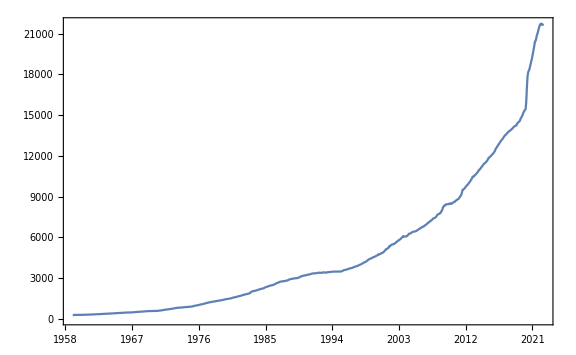

```mathematica
DateListPlot[Import["https://fred.stlouisfed.org/graph/fredgraph.csv?id=M2SL","CSV",HeaderLines->1],ImageSize->Large]
```

## APLIKACIJA V OBLAKU

```mathematica
CloudDeploy[FormPage[<|"date"->"Date"|>,CurrencyConvert[Quantity[#quantity,DatedUnit["USDollars",#date]],"USDollars"]&],"url-path",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/ts9254/url-path]